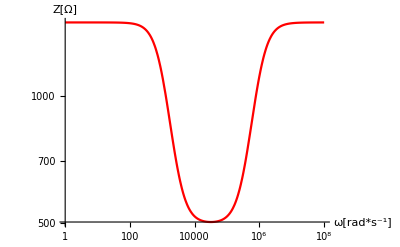

```mathematica
soucastky={
r1-> 1*10^3,
r2-> 1*10^3,
r3-> 1*10^3,
r4-> 1*10^3,
l1-> 1*10^-3,
c1-> 1*10^-6
};
impedance={
z1-> r1,
z2-> r2,
z3-> r3,
z4-> r4,
zl-> ⅉ*ω*l1,
zc-> 1/(ⅉ*ω*c1)
};
(*induktivni reaktance zl a kapacitni reaktance Zc*)

Z=(z1*zl)/(z1+zl)+(z2*zc)/(z2+zc)+(z3*z4)/(z3+z4);
res=Z/.impedance/.soucastky;
LogLogPlot[Abs[res],{ω,1,10^8},PlotStyle->Red,AxesLabel->{"ω[rad*s^-1]","Z[Ω]"}]
```